## 3.029 Spring 2022 Lecture 11 - 03/07/2022

## Polymer Reptation

Last week, we saw how we could model “stiff” polymers as correlated random walks

This week, we’ll extend our exploration to polymer dynamics and growth

In particular, we’ll investigate reptation and step-growth polymerization

This will set us up well to explore molecular dynamics next week

## Polymer Microstructures

We start by  generating non-intersecting polymer chains with correlations in 2D

We’ll then try assembling a number of them together

First - let’s write a simple function to return a polymer with N molecular units and some correlation

It will be convenient to define a “correlation” variable

Which has a value of 1 when the polymer is “maximally” correlated (i.e. the next bond angle is chosen from a range {0,0})

and a value of 0 when the polymer is uncorrelated (i.e. the next bond angle is chosen from the full range of angles {-π,π})

In-fact the maximum range is restricted further to avoid self-intersection at the trimer-level

```mathematica
Manipulate[
Graphics[{
{Blue,Circle[AngleVector[α],1/2],Dashed,Line[{{0,0},AngleVector[α]}]},
{Orange,Circle[{0,0},1/2]},
{RGBColor[0,1/3,0],Circle[AngleVector[θ+α+π],1/2],Dashed,Line[{{0,0},AngleVector[θ+α+π]}]}
}],{{α,-π,"Reference Frame Angle"},-π,π},{{θ,0,"Relative Angle"},-2π/3,2π/3},
Paneled->False]
```

```mathematica
Simplify[Rescale[correlation,{0,1},{-2π/3,0}]]
```

2/3 (-1+correlation) π

```mathematica
angularRange[correlation_]:={-1,1}(1-correlation)2π/3
```

```mathematica
angularRange[0]
```

{-(2 π)/3,(2 π)/3}

```mathematica
angularRange[1]
```

{0,0}

Let’s write a simple visualization function to help us debug

We’ll color the end-points with a different color

```mathematica
chainGraphic[sortedParticles_]:=Block[{start,end,rest,n=Length[sortedParticles],r=1/2},

{{start},rest,{end}}=TakeList[sortedParticles,{1,n-2,1}];

{
{FaceForm[None],EdgeForm[Black],Disk[#,r]&/@rest},
{FaceForm[LightGray],EdgeForm[Black],Disk[#,r]&/@{start,end}}
}
]
```

And write a simple function like the one we had last lecture

```mathematica
correlatedPolymerChain2D[numberUnits_,correlation_]:=AnglePath[RandomReal[angularRange[correlation],numberUnits-1]]
```

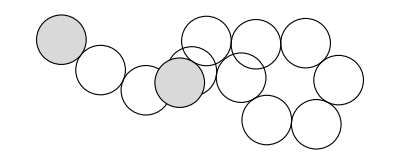

```mathematica
Graphics[chainGraphic[correlatedPolymerChain2D[12,0.4]]]
```

It’s clear this naive approach very quickly leads to self-intersections

Let’s instead write a function to append one particle at a time

while checking for collisions

Our first step is to write a collision-detection function

The simplest idea is to compute the distance b/w all the particles

And check no-distances are less the bond length

Distance between two particles

```mathematica
EuclideanDistance[{x1,y1},{x2,y2}]
```

√(Abs[x1-x2]^2+Abs[y1-y2]^2)

Distances between all particles

```mathematica
MatrixForm[Outer[EuclideanDistance,{{x1,y1},{x2,y2},{x3,y3}},{{x1,y1},{x2,y2},{x3,y3}},1]]
```

(0 | √(Abs[x1-x2]^2+Abs[y1-y2]^2) | √(Abs[x1-x3]^2+Abs[y1-y3]^2)
√(Abs[-x1+x2]^2+Abs[-y1+y2]^2) | 0 | √(Abs[x2-x3]^2+Abs[y2-y3]^2)
√(Abs[-x1+x3]^2+Abs[-y1+y3]^2) | √(Abs[-x2+x3]^2+Abs[-y2+y3]^2) | 0)

This is rather wasteful since the “Distance Matrix” is symmetric, so we only need to compute half-of it

In-fact less than half, N(N-1)/2 entries, since the diagonal is by definition 0

If you’re curious about all the ways to calculate pairwise distances in the WL - there’s a nice SE post about it here:

https://mathematica.stackexchange.com/questions/21861/fastest-way-to-calculate-matrix-of-pairwise-distances

The built-in `DistanceMatrix` function is actually reasonably fast (on numeric points using EuclideanDistance)

```mathematica
MatrixForm[DistanceMatrix[{{x1,y1},{x2,y2},{x3,y3}},DistanceFunction->EuclideanDistance]]
```

(0 | √Abs[Abs[x1-x2]^2+Abs[y1-y2]^2] | √Abs[Abs[x1-x3]^2+Abs[y1-y3]^2]
√Abs[Abs[x1-x2]^2+Abs[y1-y2]^2] | 0 | √Abs[Abs[x2-x3]^2+Abs[y2-y3]^2]
√Abs[Abs[x1-x3]^2+Abs[y1-y3]^2] | √Abs[Abs[x2-x3]^2+Abs[y2-y3]^2] | 0)

One quick common trick on Distance matrices is that often times if we want to compare distances we can just use SquaredEuclideanDistance and compare against bond_length^2

This saves us having to compute the outermost square root in all the entries above!

However, this still does more work than we need it to

Remember we’ll actually be building this polymer chain incrementally

I.e. we only need to check if the point we’re trying to add collides with any of the existing points

Since the previous points have already been checked

We can do this efficiently using `Nearest`

This uses a KDtree implementation - ask me about it if there’s time!

Essentially we’ll build a fast look-up table of the existing particles - and then find the nearest particle to our candidate

If that distance is less than the bond angle - there’s a collision

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]["Distance"]<bondLength
```

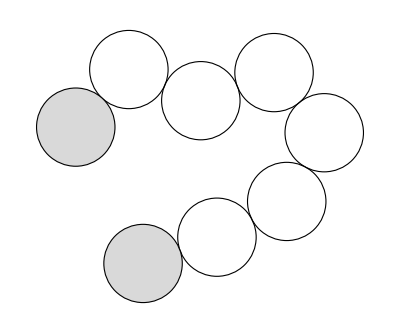

```mathematica
chainSoFar=correlatedPolymerChain2D[8,0.4];
chainGraphic[chainSoFar]//Graphics
```

Let’s debug this visually

Collision:   True

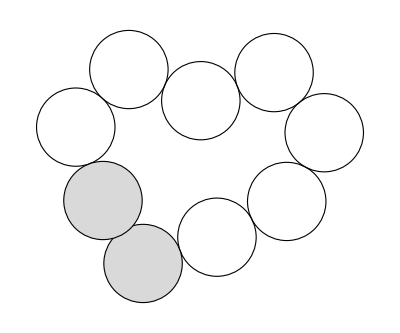

```mathematica
Block[{nf=Nearest[chainSoFar->All],lastAngle,newAngle,candidate,angleRange=angularRange[0.4]},

lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]);
newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

Echo[collisionQ[nf][candidate],"Collision: "];

chainGraphic[Append[chainSoFar,candidate]]//Graphics
]
```

Seems to work!

Let’s write this into a function

```mathematica
addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{

nf=Nearest[chainSoFar->All],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision

},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]/;Length[chainSoFar]>1
```

```mathematica
Dynamic[chainGraphic[chainSoFar]//Graphics]
```

```mathematica
Do[
chainSoFar=addCorrelatedParticleToChain[0.4][chainSoFar];
Pause[0.5],{10}]
```

Great, works as expected!

So finally, let’s wrap this in a function to compute N-molecular unit polymers

This is a job for NestWhile!

```mathematica
?NestWhile
```

```mathematica
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,maxAttempts_:100]:=NestWhile[addCorrelatedParticleToChain[correlation],correlatedPolymerChain2D[2,correlation],Length[#]<numberUnits&,1,maxAttempts]
```

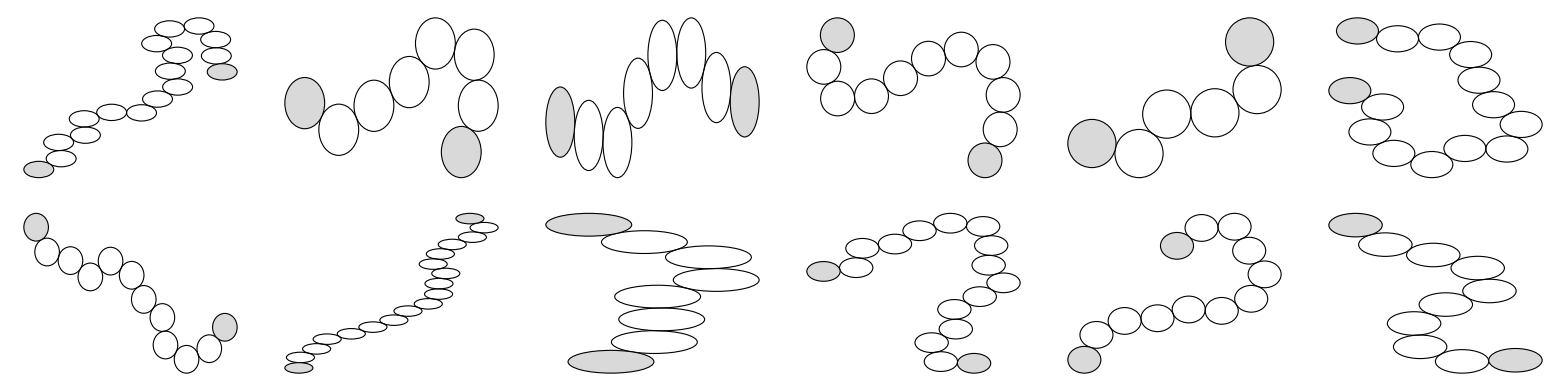

```mathematica
Multicolumn[Graphics[chainGraphic[collisionFreeCorrelatedPolymerChain2D[#,0.4]],ImageSize->200]&/@RandomInteger[{6,18},12],6,Frame->All]
```

## Polymer Reptation

We want to model the random thermal motion of a polymer chain

We consider the following simple motion:

Pick a monomer randomly from the chain, and displace it a small distance in a random direction

Move the remaining monomers in response to this

I.e. maintaining constant bond-lengths

This should be reasonable polymer motion since polymers have strong “spring-like” bonds along their backbone

### Dimer Viscous Dragging

Let’s start by considering a setup similar to our double-pendulum from L02

```mathematica
Thumbnail[,400]
```

-Graphics-

In particular, we consider a differential-algebraic system where we have:

One particle at (0,0) moving to the right at a rate s in direction α

Another particle at {Cos[β],Sin[β]}

A unit-length “rigid” rod between them with surface tension λ

```mathematica
differentialEqs={
x'[s]==λ[s] (x[s]-Cos[α]s), 
y'[s]==λ[s] (y[s]-Sin[α]s)
};

algebraicEqs={
(x[s]-Cos[α]s)^2+(y[s]-Sin[α]s)^2==1
};

initialConds[β_]={
x[0]==Cos[β],y[0]==Sin[β]
};
```

We’ll use ParametricNSolveValue again to cache our numerical solution

```mathematica
parametricNumericalSolution=ParametricNDSolveValue[{differentialEqs,algebraicEqs,initialConds[β]},{x,y,λ},{s,0,5},{α,β},Method->{"IndexReduction"->{Automatic,"IndexGoal"->0}}]
```

ParametricFunction[<>]

Let’s write a visualization function to see if this looks like a natural motion

```mathematica
visualizeDimerCartesian[α_,β0_][x_,y_][s_]:=
Graphics[{
{Red,Dashed,Arrow[{{0,0},2AngleVector[α]}],Circle[{0,0},1/2],Disk[{Cos[α]s,Sin[α]s},1/2]},
{Blue,Dashed,Circle[AngleVector[β0],1/2],Disk[{x[s],y[s]},1/2]}
},PlotRange->2{{-1,1},{-1,1}}]
```

```mathematica
Manipulate[
DynamicModule[{f=visualizeDimerCartesian[α,β0][#1,#2]&@@parametricNumericalSolution[α,β0]},
Animate[f[s],{{s,0,"Displacement"},0,3},AnimationRunning->False,Paneled->False]
],
{{α,π/4,"Angle of Motion"},-π,π},{{β0,-π/3,"Initial Angle of Second Particle"},-π,π},Paneled->False]
```

Great, this looks reasonable

Even though we’ve cached our numerical results

this will still be too slow for our purposes

as such we look for a symbolic solution

In-fact, switching to generalized coordinates leads to the simpler equation

β'(s) == (1-ν)Sin[β(s)]

Where we’ve introduced a “stickiness” coefficient ν

```mathematica
angleBetweenParticles[ν_,β0_][s_]=DSolveValue[{D[β[s],s]== (1-ν) Sin[β[s]],β[0]==β0},β[s],s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2 ArcCot[ⅇ^(-s+s ν) Cot[β0/2]]

For ν=0, the two solutions coincide!

```mathematica
visualizeDimer[α_,β0_,ν_:0][s_]:=
Graphics[{
{Red,Dashed,Arrow[{{0,0},2AngleVector[α]}],Circle[{0,0},1/2],Disk[{Cos[α]s,Sin[α]s},1/2]},
{RGBColor[0,1/3,0],Circle[RotationTransform[α][{s,0} + AngleVector[angleBetweenParticles[ν,β0-α][s]]],1/2],Dashed,Circle[AngleVector[β0],1/2],Disk[RotationTransform[α][{s,0} + AngleVector[angleBetweenParticles[ν,β0-α][s]]],1/2,{-π/2,π/2}]}
},PlotRange->2{{-1,1},{-1,1}}]
```

```mathematica
Manipulate[
DynamicModule[{f=visualizeDimerCartesian[α,β0][#1,#2]&@@parametricNumericalSolution[α,β0]},
Animate[Show[f[s],visualizeDimer[α,β0,ν][s]],{{s,0,"Displacement"},0,3},AnimationRunning->False,Paneled->False]
],{{ν,0,"Stickiness"},0,1},
{{α,π/4,"Angle of Motion"},-π,π},{{β0,-π/3,"Initial Angle of Second Particle"},-π,π},Paneled->False]
```

### Polymer Viscous Dragging

We can work out the conditions for dragging multiple particles

E.g. 5 particles being dragged by particle #3

Note, the angles go like this: β21, β32,β33,β34,β45

```mathematica
DynamicModule[{d1,d2,d3,d4,d5, β33 =0,β=angleBetweenParticles},
Manipulate[
Graphics[
d3 = s AngleVector[β[ν,β33][s]];
d4 = d3 + AngleVector[β[ν,β34-θ][s]];
d5 = d4 + AngleVector[β[ν,β45-θ][s]];
d2 = d3 + AngleVector[β[ν,β32-θ][s]];
d1 = d2 + AngleVector[β[ν,β21-θ][s]];

{Blue,Arrow[{{0,0},AngleVector[θ]}],
Circle[RotationMatrix[θ].d3,1/2],
Orange,
Circle[RotationMatrix[θ].d4,1/2],
Circle[RotationMatrix[θ].d5,1/2],
Circle[RotationMatrix[θ].d2,1/2],
Circle[RotationMatrix[θ].d1,1/2]
,Black,
Text[1,RotationMatrix[θ].d1],
Text[2,RotationMatrix[θ].d2],
Text[3,RotationMatrix[θ].d3],
Text[4,RotationMatrix[θ].d4],
Text[5,RotationMatrix[θ].d5]


},
PlotRange->3{{-1,1},{-1,1}},Frame->True
],
{{ν,0,"Stickiness"},0,1},
{{θ,0,"Angle of Motion"},0, 2Pi},
{{s,0,"Displacement"},0,1},
{β45,-Pi,Pi},
{{β34,Pi/2},-Pi,Pi},
{{β32,-1},-Pi,Pi},
{{β21,-1},-Pi,Pi},Paneled->False
]
]
```

Let’s see how we can generalize this

```mathematica
Block[{d1,d2,d3,d4,d5, β33 =0,β=angleBetweenParticles},
β33=0;
d3 = s AngleVector[β[ν,β33][s]];
d4 = d3 + AngleVector[β[ν,β34-θ][s]];
d5 = d4 + AngleVector[β[ν,β45-θ][s]];
d2 = d3 + AngleVector[β[ν,β32-θ][s]];
d1 = d2 + AngleVector[β[ν,β21-θ][s]];
RotationTransform[θ][{d1,d2,d3,d4,d5}]//Grid
]
```

Cos[θ] (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β21-θ)/2]]]+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]])-Sin[θ] (Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β21-θ)/2]]]+Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]]) | (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β21-θ)/2]]]+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]]) Sin[θ]+Cos[θ] (Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β21-θ)/2]]]+Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]])
Cos[θ] (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]])-Sin[θ] Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]] | (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]]) Sin[θ]+Cos[θ] Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β32-θ)/2]]]
s Cos[θ] | s Sin[θ]
Cos[θ] (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]])-Sin[θ] Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]] | (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]) Sin[θ]+Cos[θ] Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]
Cos[θ] (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β45-θ)/2]]])-Sin[θ] (Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]+Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β45-θ)/2]]]) | (s+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]+Cos[2 ArcCot[ⅇ^(-s+s ν) Cot[(β45-θ)/2]]]) Sin[θ]+Cos[θ] (Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β34-θ)/2]]]+Sin[2 ArcCot[ⅇ^(-s+s ν) Cot[(β45-θ)/2]]])

We notice these all have the same general form:

Namely involve factors of θ + 2 ArcCot[ⅇ^(s ⋁ -s)Cos[(β-θ)/2]]

These get used over and over again, so it will be beneficial for us to precompute them

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

Similarly, we write a recursive function to propagate these outwards from the perturbed index

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },

Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]
```

Notice the function does three main things:

Precompute the costly trigonometric functions

Define the recursion base-case

I.e. move the perturbed particle a distance s along the direction θ

And then define the recursive function to either advance or decrease the index to sample the precomputed distances

### Self-avoiding Reptation

Let’s wrap this all together in a single-chain reptation function

```mathematica
moveSingleChainRandomly[ positions_,ds_,stickiness_:0.1]:= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]]
```

```mathematica
chainPositions=collisionFreeCorrelatedPolymerChain2D[8,0.4];
chainPositions=TranslationTransform[-Mean[chainPositions]][chainPositions];
Dynamic[Graphics[chainGraphic[chainPositions],PlotRange->10{{-1,1},{-1,1}}]]
```

```mathematica
Do[
chainPositions=moveSingleChainRandomly[chainPositions,0.1];
Pause[0.1],
{100}]
```

Notice we’ll still run into the same issue of self-intersections when the polymer chains are long

We’ll brute-force a collision detection scheme again

I.e. take a step, and only accept it if it doesn’t result in collisions

We use a simple collision detection

I.e. we check for all particles within a radius of 1-ϵ at each position

And make sure that length is equal to the number of particles

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]
```

```mathematica
moveSingleChain[ positions_,ds_,stickiness_:0.1]:= 
Block[{newPositions},
newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];
If[collisionFreeQ[newPositions],newPositions,positions]
]
```

```mathematica
chainPositions=collisionFreeCorrelatedPolymerChain2D[24,0.4];
chainPositions=TranslationTransform[-Mean[chainPositions]][chainPositions];
Dynamic[Graphics[chainGraphic[chainPositions],PlotRange->15{{-1,1},{-1,1}}]]
```

```mathematica
Do[
chainPositions=moveSingleChain[chainPositions,0.1];
Pause[0.1],
{100}]
```